```mathematica
(*Notebook takes vertical and horizontal deformations of the gel as well as bound copper generated from strong_acid_2D.mph and applies them to coarser rectangular mesh of the same dimenions for better visualization*)
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
SetDirectory["/media/chinobangs/easystore/Final_sim_07_02/2d_simulations_final"]
(*put your current working directory with the exports from comsol in the command above*)
```

```mathematica
verticaldef = ImportString[
StringReplace[Import["ver_def_strong_0.1_figure_3.txt", "Text"],
StartOfLine~~"%"~~Shortest[___]~~EndOfLine~~"\n"->""],"Table"];
(*vertical deformation profile at t=0.1 \tau. See Export in strong_acid_2D.mph*)
```

```mathematica
baddata[entry_]:=Not[MatchQ[entry[[3]],_?NumberQ]];
verticaldef=DeleteCases[verticaldef,_?baddata];
noofcol = Length[verticaldef[[1,All]]];
noofrow = Length[verticaldef];
```

```mathematica
horizontaldef = ImportString[
StringReplace[Import["hor_def_strong_0.1_figure_3.txt", "Text"],
StartOfLine~~"%"~~Shortest[___]~~EndOfLine~~"\n"->""],"Table"];
(*horizontal deformation profile at t=0.1\tau. See Export in strong_acid_2D.mph*)
```

```mathematica
horizontaldef=DeleteCases[horizontaldef,_?baddata];
```

```mathematica
xcoord= verticaldef[[All,1]];
ycoord= horizontaldef[[All,2]];
xdef= horizontaldef[[All,3]];
ydef= verticaldef[[All,3]];
```

```mathematica
<<NDSolve`FEM`
```

```mathematica
nx=2500;ny=2500;
{xStart,xStop}={0,1};
{yStart,yStop}={0,1};
coordinates=Flatten[Table[{x,y},{y,yStart,yStop,(yStop-yStart)/ny},{x,xStart,xStop,(xStop-xStart)/nx}],1];
incidents=Flatten[Table[{(j-1)*(nx+1)+i,(j-1)*(nx+1)+i+1,j*(nx+1)+i+1,j*(nx+1)+i},{j,1,ny},{i,1,nx}],1];
m2=ToElementMesh["Coordinates"->coordinates,"MeshElements"->{QuadElement[incidents]}];
```

```mathematica
coord = Transpose[{xcoord,ycoord}];
coord=coord+RandomReal[{-10^-9,10^-9},{Length[coord]}];
```

```mathematica
datavert =Table[Transpose[{coord,ydef}]];
ydeffunc = Interpolation[datavert,InterpolationOrder->1];
```

```mathematica
datahor = Table[Transpose[{coord,xdef}]];
xdeffunc = Interpolation[datahor,InterpolationOrder->1];
```

```mathematica
ydeffuncnew[coordinates_]:=Map[ydeffunc[#[[1]],#[[2]]]&,coordinates];
vif = ElementMeshInterpolation[{m2},ydeffuncnew[m2["Coordinates"]]];
```

InterpolatingFunction::femdmval: Input value {0.,0.} lies outside the range of data in the interpolating function.

InterpolatingFunction::femdmval: Input value {0.0004,0.} lies outside the range of data in the interpolating function.

InterpolatingFunction::femdmval: Input value {0.9988,0.} lies outside the range of data in the interpolating function.

General::stop: Further output of InterpolatingFunction::femdmval will be suppressed during this calculation.

```mathematica
xdeffuncnew[coordinates_]:=Map[xdeffunc[#[[1]],#[[2]]]&,coordinates];
uif = ElementMeshInterpolation[{m2},xdeffuncnew[m2["Coordinates"]]];
```

InterpolatingFunction::femdmval: Input value {0.,0.} lies outside the range of data in the interpolating function.

InterpolatingFunction::femdmval: Input value {0.0004,0.} lies outside the range of data in the interpolating function.

InterpolatingFunction::femdmval: Input value {0.9988,0.} lies outside the range of data in the interpolating function.

General::stop: Further output of InterpolatingFunction::femdmval will be suppressed during this calculation.

```mathematica
nm=ElementMeshDeformation[m2,{uif,vif}];
meshcoord=nm["Coordinates"];
```

```mathematica
coarsefactory = 500;
coarsefactorx=100;
l ={};
Do[AppendTo[l,meshcoord[[i*coarsefactorx+1;;(nx+1)*ny+i*coarsefactorx+1;;nx+1]]],{i,0,nx/coarsefactorx}];
Do[AppendTo[l,meshcoord[[j*(nx+1)*coarsefactory+1;;j*(nx+1)*coarsefactory+(nx+1)]]],{j,0,ny/coarsefactory}];
res=ListLinePlot[l,InterpolationOrder->3, PlotStyle->{{Thickness[0.003],GrayLevel[0]}},Axes->False, AspectRatio->0.4,ImageSize->{1000,400},PlotRange->{{0,1},{-0.000001,2}},Frame-> False, PlotRangePadding->None, ImageMargins->0]
```

-Graphics-

```mathematica
omega = ImplicitRegion[True,{{x,0,1},{y,0,1}}];
```

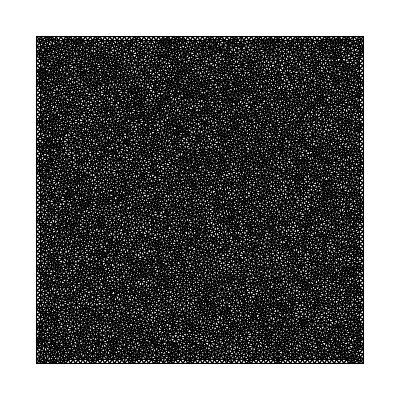

```mathematica
nm2=ToElementMesh[omega,MaxCellMeasure->0.0001];
nm2["Wireframe"]
```

```mathematica
boundcopp = ImportString[
StringReplace[Import["bound_copper_strong_0.1_figure_3.txt", "Text"],
StartOfLine~~"%"~~Shortest[___]~~EndOfLine~~"\n"->""],"Table"];
(*bound copper profile at t=0.1\tau. See Export in strong_acid_2D.mph*)
```

```mathematica
boundcopp=DeleteCases[boundcopp,_?baddata];
```

```mathematica
bcvolfrac= boundcopp[[All,3]];
```

```mathematica
databc =Table[Transpose[{coord,bcvolfrac}]];
bcfunc = Interpolation[databc,InterpolationOrder->1];
```

```mathematica
bcfuncnew[coordinates_]:=Map[bcfunc[#[[1]],#[[2]]]&,coordinates];
bcif = ElementMeshInterpolation[{nm2},bcfuncnew[nm2["Coordinates"]]];
```

InterpolatingFunction::femdmval: Input value {0.,0.} lies outside the range of data in the interpolating function.

InterpolatingFunction::femdmval: Input value {0.,1.} lies outside the range of data in the interpolating function.

InterpolatingFunction::femdmval: Input value {1.,0.} lies outside the range of data in the interpolating function.

General::stop: Further output of InterpolatingFunction::femdmval will be suppressed during this calculation.

```mathematica
vif2 = ElementMeshInterpolation[{nm2},ydeffuncnew[nm2["Coordinates"]]];
```

InterpolatingFunction::femdmval: Input value {0.,0.} lies outside the range of data in the interpolating function.

InterpolatingFunction::femdmval: Input value {0.,1.} lies outside the range of data in the interpolating function.

InterpolatingFunction::femdmval: Input value {1.,0.} lies outside the range of data in the interpolating function.

General::stop: Further output of InterpolatingFunction::femdmval will be suppressed during this calculation.

```mathematica
uif2 = ElementMeshInterpolation[{nm2},xdeffuncnew[nm2["Coordinates"]]];
```

InterpolatingFunction::femdmval: Input value {0.,0.} lies outside the range of data in the interpolating function.

InterpolatingFunction::femdmval: Input value {0.,1.} lies outside the range of data in the interpolating function.

InterpolatingFunction::femdmval: Input value {1.,0.} lies outside the range of data in the interpolating function.

General::stop: Further output of InterpolatingFunction::femdmval will be suppressed during this calculation.

```mathematica
nm3=ElementMeshDeformation[nm2,{uif2,vif2}];
```

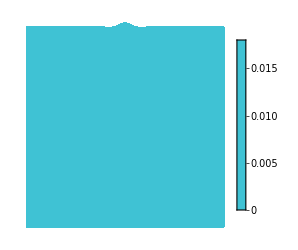

```mathematica
res2=DensityPlot[bcif[x,y],{x,y}∈nm3,PlotRange->All,ColorFunction->(Hue[0.52,0.7,0.83,Rescale[#1,{0,0.018}]]&),ColorFunctionScaling->False,ImageSize->{250,500},PlotRange->{{0,1},{-0.00000001,2}},PlotLegends->BarLegend[{Hue[0.52,0.7,0.83,Rescale[#1,{0,0.018}]]&,{0,0.018}}],Frame->False]
```

```mathematica
Show[res2,res,PlotRange->{{0,1},{-0.000001,2}},AspectRatio->0.4,ImageSize->{1000,400},Frame->False,PlotRangePadding->None,PlotRangeClipping->True]
(*save the plot as "deform_strong_0.1_figure_3.png" by right clicking-> save graphic as*)
```

-Graphics-